```mathematica
RegisterExternalEvaluator["Python","C:\\Python36\\python.exe"]
```

eaaf7220-d73d-496b-b9a9-2a191ab62c66

```mathematica
dir="\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2020\\02\\03\\2020-02-01-17-52-48";
SetDirectory[dir];
file=FileNames["*.pkl"]
```

{outside_forward_log10.pkl,outside_forward_log11.pkl,outside_forward_log12.pkl,outside_forward_log13.pkl,outside_forward_log14.pkl,outside_forward_log15.pkl,outside_forward_log16.pkl,outside_forward_log17.pkl,outside_forward_log18.pkl,outside_forward_log19.pkl,outside_forward_log1.pkl,outside_forward_log2.pkl,outside_forward_log3.pkl,outside_forward_log4.pkl,outside_forward_log5.pkl,outside_forward_log6.pkl,outside_forward_log7.pkl,outside_forward_log8.pkl,outside_forward_log9.pkl,outside_reverse_log1.pkl,outside_reverse_log2.pkl,outside_reverse_log3.pkl}

```mathematica
data=ExternalEvaluate["Python", "import pickle; import sys; sys.path.append('<>dir<>'); f= open('"<>#<>"', 'rb'); data = pickle.load(f); data"] &/@file;
```

```mathematica
Keys[data⟦1⟧]
```

{value_LRRG_CAVITY_REVERSE_POWER_0,EVID_KLYSTRON_REVERSE_PHASE_-1,EVID_KLYSTRON_REVERSE_PHASE_-2,vacuum,EVID_KLYSTRON_REVERSE_POWER_0,EVID_KLYSTRON_REVERSE_POWER_1,num_events,EVID_KLYSTRON_FORWARD_PHASE_2,EVID_KLYSTRON_FORWARD_PHASE_1,EVID_KLYSTRON_FORWARD_PHASE_0,EVID_LRRG_CAVITY_REVERSE_POWER_-2,EVID_LRRG_CAVITY_REVERSE_POWER_-1,lo_mask_KLYSTRON_REVERSE_PHASE,time_LRRG_CAVITY_FORWARD_POWER_-2,time_LRRG_CAVITY_FORWARD_POWER_-1,EVID_KLYSTRON_FORWARD_POWER_-2,name_KLYSTRON_REVERSE_POWER_-1,name_KLYSTRON_REVERSE_POWER_-2,value_LRRG_CAVITY_REVERSE_PHASE_1,value_LRRG_CAVITY_REVERSE_PHASE_0,value_LRRG_CAVITY_REVERSE_PHASE_2,value_KLYSTRON_FORWARD_POWER_-1,mask_floor,value_KLYSTRON_FORWARD_POWER_-2,time_KLYSTRON_FORWARD_PHASE_0,time_KLYSTRON_FORWARD_PHASE_1,time_KLYSTRON_FORWARD_PHASE_2,value_KLYSTRON_FORWARD_POWER_1,value_KLYSTRON_FORWARD_POWER_0,value_KLYSTRON_FORWARD_POWER_2,lo_mask_LRRG_CAVITY_FORWARD_PHASE,hi_mask_LRRG_CAVITY_FORWARD_POWER,EVID_LRRG_CAVITY_FORWARD_PHASE_-2,name_KLYSTRON_REVERSE_PHASE_2,name_KLYSTRON_REVERSE_PHASE_1,name_KLYSTRON_REVERSE_PHASE_0,time_vector,value_LRRG_CAVITY_FORWARD_PHASE_-2,hi_mask_LRRG_CAVITY_REVERSE_POWER,EVID_LRRG_CAVITY_FORWARD_POWER_1,time_KLYSTRON_FORWARD_PHASE_-2,EVID_KLYSTRON_REVERSE_POWER_2,name_LRRG_CAVITY_REVERSE_PHASE_-2,time_KLYSTRON_FORWARD_PHASE_-1,name_KLYSTRON_FORWARD_PHASE_2,value_KLYSTRON_FORWARD_PHASE_-2,value_KLYSTRON_FORWARD_PHASE_-1,time_LRRG_CAVITY_FORWARD_PHASE_-1,time_LRRG_CAVITY_FORWARD_PHASE_-2,time_KLYSTRON_FORWARD_POWER_2,name_KLYSTRON_FORWARD_PHASE_0,time_KLYSTRON_FORWARD_POWER_0,time_KLYSTRON_FORWARD_POWER_1,name_KLYSTRON_FORWARD_PHASE_1,time_LRRG_CAVITY_FORWARD_POWER_1,EVID_LRRG_CAVITY_REVERSE_POWER_2,time_LRRG_CAVITY_FORWARD_POWER_0,hi_mask_KLYSTRON_FORWARD_POWER,lo_mask_KLYSTRON_REVERSE_POWER,hi_mask_KLYSTRON_REVERSE_POWER,EVID_LRRG_CAVITY_FORWARD_PHASE_1,EVID_LRRG_CAVITY_FORWARD_PHASE_2,hi_mask_KLYSTRON_FORWARD_PHASE,value_KLYSTRON_REVERSE_PHASE_2,value_KLYSTRON_REVERSE_PHASE_0,value_KLYSTRON_REVERSE_PHASE_1,time_LRRG_CAVITY_REVERSE_POWER_-1,time_LRRG_CAVITY_REVERSE_POWER_-2,EVID_KLYSTRON_FORWARD_POWER_-1,value_LRRG_CAVITY_REVERSE_POWER_-2,value_LRRG_CAVITY_REVERSE_POWER_-1,EVID_LRRG_CAVITY_FORWARD_PHASE_-1,name_KLYSTRON_FORWARD_PHASE_-1,name_KLYSTRON_FORWARD_PHASE_-2,time_LRRG_CAVITY_REVERSE_PHASE_1,EVID_LRRG_CAVITY_REVERSE_PHASE_-1,time_KLYSTRON_REVERSE_PHASE_1,time_KLYSTRON_REVERSE_PHASE_0,time_KLYSTRON_REVERSE_PHASE_2,value_KLYSTRON_REVERSE_POWER_-2,value_KLYSTRON_REVERSE_POWER_-1,time_LRRG_CAVITY_REVERSE_PHASE_0,name_KLYSTRON_REVERSE_PHASE_-2,name_KLYSTRON_REVERSE_PHASE_-1,EVID_LRRG_CAVITY_REVERSE_PHASE_-2,name_LRRG_CAVITY_REVERSE_POWER_0,name_LRRG_CAVITY_REVERSE_POWER_1,EVID_LRRG_CAVITY_REVERSE_POWER_1,EVID_LRRG_CAVITY_REVERSE_POWER_0,num_collected_traces,EVID_LRRG_CAVITY_FORWARD_PHASE_0,value_KLYSTRON_FORWARD_PHASE_2,value_KLYSTRON_FORWARD_PHASE_1,value_KLYSTRON_FORWARD_PHASE_0,EVID_KLYSTRON_FORWARD_PHASE_-2,EVID_KLYSTRON_FORWARD_PHASE_-1,time_LRRG_CAVITY_REVERSE_PHASE_-2,time_LRRG_CAVITY_REVERSE_PHASE_-1,name_KLYSTRON_FORWARD_POWER_-2,value_KLYSTRON_REVERSE_PHASE_-1,value_KLYSTRON_REVERSE_PHASE_-2,name_KLYSTRON_FORWARD_POWER_-1,name_LRRG_CAVITY_FORWARD_PHASE_-2,name_LRRG_CAVITY_REVERSE_PHASE_2,name_LRRG_CAVITY_REVERSE_PHASE_0,name_LRRG_CAVITY_REVERSE_PHASE_1,time_LRRG_CAVITY_FORWARD_PHASE_1,name_LRRG_CAVITY_FORWARD_PHASE_-1,time_LRRG_CAVITY_FORWARD_PHASE_2,name_LRRG_CAVITY_FORWARD_PHASE_2,time_KLYSTRON_REVERSE_POWER_-2,time_KLYSTRON_REVERSE_POWER_-1,EVID_KLYSTRON_FORWARD_POWER_1,EVID_KLYSTRON_FORWARD_POWER_0,EVID_KLYSTRON_FORWARD_POWER_2,time_KLYSTRON_REVERSE_POWER_2,time_KLYSTRON_REVERSE_POWER_1,time_KLYSTRON_REVERSE_POWER_0,EVID_KLYSTRON_REVERSE_POWER_-2,EVID_KLYSTRON_REVERSE_POWER_-1,name_LRRG_CAVITY_REVERSE_POWER_2,value_LRRG_CAVITY_FORWARD_POWER_-1,value_LRRG_CAVITY_FORWARD_POWER_-2,value_LRRG_CAVITY_FORWARD_PHASE_0,message,hi_mask_KLYSTRON_REVERSE_PHASE,trace_name,name_LRRG_CAVITY_FORWARD_PHASE_1,name_LRRG_CAVITY_FORWARD_PHASE_0,time_LRRG_CAVITY_FORWARD_PHASE_0,EVID_LRRG_CAVITY_REVERSE_PHASE_1,EVID_LRRG_CAVITY_REVERSE_PHASE_0,hi_mask_LRRG_CAVITY_FORWARD_PHASE,EVID_LRRG_CAVITY_REVERSE_PHASE_2,name_KLYSTRON_FORWARD_POWER_0,name_KLYSTRON_FORWARD_POWER_1,name_KLYSTRON_FORWARD_POWER_2,time_LRRG_CAVITY_REVERSE_PHASE_2,name_KLYSTRON_REVERSE_POWER_1,name_KLYSTRON_REVERSE_POWER_0,name_KLYSTRON_REVERSE_POWER_2,hi_mask_LRRG_CAVITY_REVERSE_PHASE,EVID_LRRG_CAVITY_FORWARD_POWER_2,EVID_LRRG_CAVITY_FORWARD_POWER_0,value_LRRG_CAVITY_FORWARD_PHASE_-1,time_KLYSTRON_REVERSE_PHASE_-1,time_KLYSTRON_REVERSE_PHASE_-2,is_collecting,value_LRRG_CAVITY_REVERSE_PHASE_-1,value_LRRG_CAVITY_FORWARD_PHASE_1,value_LRRG_CAVITY_FORWARD_PHASE_2,value_LRRG_CAVITY_REVERSE_PHASE_-2,EVID_KLYSTRON_REVERSE_PHASE_2,DC,EVID_KLYSTRON_REVERSE_PHASE_0,EVID_KLYSTRON_REVERSE_PHASE_1,time_LRRG_CAVITY_FORWARD_POWER_2,outside_mask_index,value_KLYSTRON_REVERSE_POWER_0,value_KLYSTRON_REVERSE_POWER_1,value_KLYSTRON_REVERSE_POWER_2,lo_mask_KLYSTRON_FORWARD_POWER,time_LRRG_CAVITY_REVERSE_POWER_2,time_LRRG_CAVITY_REVERSE_POWER_0,time_LRRG_CAVITY_REVERSE_POWER_1,name_LRRG_CAVITY_FORWARD_POWER_1,name_LRRG_CAVITY_FORWARD_POWER_0,value_LRRG_CAVITY_REVERSE_POWER_1,name_LRRG_CAVITY_FORWARD_POWER_2,name_LRRG_CAVITY_FORWARD_POWER_-1,SOL,time_KLYSTRON_FORWARD_POWER_-1,time_KLYSTRON_FORWARD_POWER_-2,lo_mask_KLYSTRON_FORWARD_PHASE,name_LRRG_CAVITY_FORWARD_POWER_-2,EVID_LRRG_CAVITY_FORWARD_POWER_-1,EVID_LRRG_CAVITY_FORWARD_POWER_-2,name_LRRG_CAVITY_REVERSE_POWER_-2,name_LRRG_CAVITY_REVERSE_POWER_-1,lo_mask_LRRG_CAVITY_REVERSE_POWER,lo_mask_LRRG_CAVITY_REVERSE_PHASE,value_LRRG_CAVITY_FORWARD_POWER_2,value_LRRG_CAVITY_FORWARD_POWER_0,value_LRRG_CAVITY_FORWARD_POWER_1,lo_mask_LRRG_CAVITY_FORWARD_POWER,value_LRRG_CAVITY_REVERSE_POWER_2,name_LRRG_CAVITY_REVERSE_PHASE_-1}

```mathematica
CRPkeys=Sort[Select[Keys[data⟦1⟧],StringContainsQ[#,"value_LRRG_CAVITY_REVERSE_POWER_"]&]]
CFPkeys=Sort[Select[Keys[data⟦1⟧],StringContainsQ[#,"value_LRRG_CAVITY_FORWARD_POWER_"]&]]
KRPkeys=Sort[Select[Keys[data⟦1⟧],StringContainsQ[#,"value_KLYSTRON_REVERSE_POWER_"]&]]
KFPkeys=Sort[Select[Keys[data⟦1⟧],StringContainsQ[#,"value_KLYSTRON_FORWARD_POWER_"]&]]
CRPhakeys=Sort[Select[Keys[data⟦1⟧],StringContainsQ[#,"value_LRRG_CAVITY_REVERSE_PHASE_"]&]]
CFPhakeys=Sort[Select[Keys[data⟦1⟧],StringContainsQ[#,"value_LRRG_CAVITY_FORWARD_PHASE_"]&]]
KRPhakeys=Sort[Select[Keys[data⟦1⟧],StringContainsQ[#,"value_KLYSTRON_REVERSE_PHASE_"]&]]
KFPhakeys=Sort[Select[Keys[data⟦1⟧],StringContainsQ[#,"value_KLYSTRON_FORWARD_PHASE_"]&]]
```

{value_LRRG_CAVITY_REVERSE_POWER_0,value_LRRG_CAVITY_REVERSE_POWER_-1,value_LRRG_CAVITY_REVERSE_POWER_1,value_LRRG_CAVITY_REVERSE_POWER_-2,value_LRRG_CAVITY_REVERSE_POWER_2}

{value_LRRG_CAVITY_FORWARD_POWER_0,value_LRRG_CAVITY_FORWARD_POWER_-1,value_LRRG_CAVITY_FORWARD_POWER_1,value_LRRG_CAVITY_FORWARD_POWER_-2,value_LRRG_CAVITY_FORWARD_POWER_2}

{value_KLYSTRON_REVERSE_POWER_0,value_KLYSTRON_REVERSE_POWER_-1,value_KLYSTRON_REVERSE_POWER_1,value_KLYSTRON_REVERSE_POWER_-2,value_KLYSTRON_REVERSE_POWER_2}

{value_KLYSTRON_FORWARD_POWER_0,value_KLYSTRON_FORWARD_POWER_-1,value_KLYSTRON_FORWARD_POWER_1,value_KLYSTRON_FORWARD_POWER_-2,value_KLYSTRON_FORWARD_POWER_2}

{value_LRRG_CAVITY_REVERSE_PHASE_0,value_LRRG_CAVITY_REVERSE_PHASE_-1,value_LRRG_CAVITY_REVERSE_PHASE_1,value_LRRG_CAVITY_REVERSE_PHASE_-2,value_LRRG_CAVITY_REVERSE_PHASE_2}

{value_LRRG_CAVITY_FORWARD_PHASE_0,value_LRRG_CAVITY_FORWARD_PHASE_-1,value_LRRG_CAVITY_FORWARD_PHASE_1,value_LRRG_CAVITY_FORWARD_PHASE_-2,value_LRRG_CAVITY_FORWARD_PHASE_2}

{value_KLYSTRON_REVERSE_PHASE_0,value_KLYSTRON_REVERSE_PHASE_-1,value_KLYSTRON_REVERSE_PHASE_1,value_KLYSTRON_REVERSE_PHASE_-2,value_KLYSTRON_REVERSE_PHASE_2}

{value_KLYSTRON_FORWARD_PHASE_0,value_KLYSTRON_FORWARD_PHASE_-1,value_KLYSTRON_FORWARD_PHASE_1,value_KLYSTRON_FORWARD_PHASE_-2,value_KLYSTRON_FORWARD_PHASE_2}

```mathematica
powkeylist={CRPkeys,CFPkeys,KRPkeys,KFPkeys};
phakeylist={CRPhakeys,CFPhakeys,KRPhakeys,KFPhakeys};
```

```mathematica
powdat=Table[Table[Select[data⟦i⟧[#]&/@keylist⟦j⟧,#⟦200⟧>10000&],{i,1,Length@data}],{j,1,Length@powkeylist}];
phadat=Table[Table[Select[data⟦i⟧[#]&/@keylist⟦j⟧,#⟦200⟧>10000&],{i,1,Length@data}],{j,1,Length@powkeylist}];
```

```mathematica
Length/@tdat⟦5⟧
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Total/@Transpose[tdat⟦1⟧]
```

Transpose::nmtx: The first two levels of {{{4.15169,2.87453,1.46058,1.025,1.53052,1.00496,1.00496,1.00496,1.39369,2.35576,3.17599,4.80675,1.66726,«25»,27.0327,25.7828,18.5311,9.39841,6.82802,6.96007,4.67732,3.64661,3.98406,4.29391,6.24977,11.1673,«967»}},«21»} cannot be transposed.

Total::tllen: Lists of unequal length in {{{4.15169,2.87453,1.46058,1.025,1.53052,1.00496,1.00496,1.00496,1.39369,2.35576,3.17599,4.80675,1.66726,«25»,27.0327,25.7828,18.5311,9.39841,6.82802,6.96007,4.67732,3.64661,3.98406,4.29391,6.24977,11.1673,«967»}},«21»} cannot be added.

Transpose[Total[{{{4.15169,2.87453,1.46058,1.025,1.53052,1.00496,1.00496,1.00496,1.39369,2.35576,3.17599,995,1.7336,1.63931,1.79331,1.01329,0.663994,0.650975,0.377565,0.171871,0.171871,0.454757,0.50776}},20,{1}}]]
 |  |  |  |

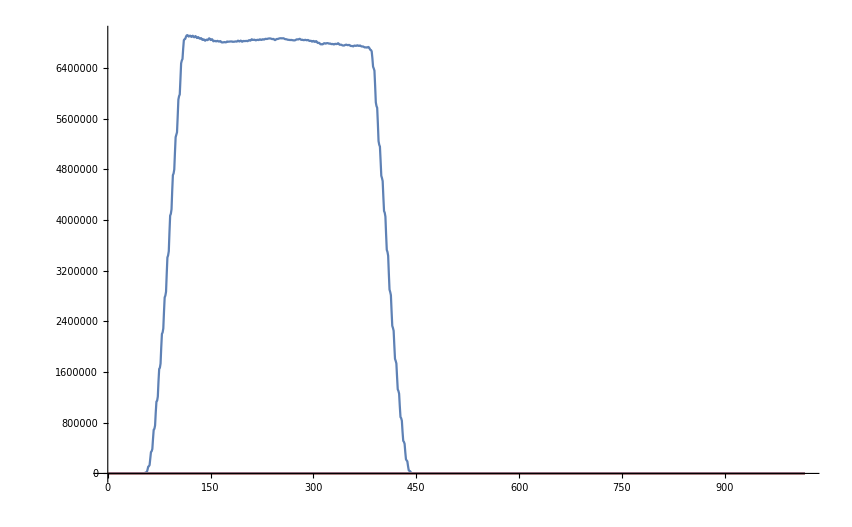

```mathematica
ListLinePlot[data⟦3⟧[#]&/@KFPkeys, PlotRange->All]
```

```mathematica
RegisterExternalEvaluator["Python","C:\\Python27\\python.exe"]
```

RegisterExternalEvaluator::invalid: -- Message text not found -- (ExternalEvaluate`Private`reason)

$Failed

```mathematica
dir="\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2020\\02\\14\\2020-02-14-23-40-15";
SetDirectory[dir];
file=FileNames["*.pkl"]
```

{vac_spike_monitor_1.pkl,vac_spike_monitor_2.pkl,vac_spike_monitor_3.pkl}

```mathematica
data1=ExternalEvaluate["Python", "import pickle; import sys; sys.path.append('<>dir<>'); f= open('"<>file⟦1⟧<>"', 'rb'); data = pickle.load(f); data"] ;
data2=ExternalEvaluate["Python", "import pickle; import sys; sys.path.append('<>dir<>'); f= open('"<>file⟦2⟧<>"', 'rb'); data = pickle.load(f); data"] ;
data3=ExternalEvaluate["Python", "import pickle; import sys; sys.path.append('<>dir<>'); f= open('"<>file⟦3⟧<>"', 'rb'); data = pickle.load(f); data"] ;
```

```mathematica
Lookup[data1,"LRRG_CAVITY_REVERSE_POWER_0_timestamp"]
Lookup[data2,"LRRG_CAVITY_REVERSE_POWER_0_timestamp"]
Lookup[data3,"LRRG_CAVITY_REVERSE_POWER_0_timestamp"]
```

Fri Feb 14 2020 23:45:25.592724536

Fri Feb 14 2020 23:55:01.458976803

Sat Feb 15 2020 00:07:00.767049850

```mathematica
Sort[Select[Keys[data3],StringContainsQ[#,"LRRG_CAVITY_REVERSE_POWER"]∧StringContainsQ[#,"time"]&]]⟦1⟧
Sort[Select[Keys[data3],StringContainsQ[#,"LRRG_CAVITY_REVERSE_POWER"]∧StringContainsQ[#,"time"]&]]⟦1⟧
```

LRRG_CAVITY_REVERSE_POWER_0_timestamp

LRRG_CAVITY_REVERSE_POWER_0_timestamp

```mathematica
KFPkeys=Table["KLYSTRON_FORWARD_POWER_"<>ToString@i<>"_data",{i,0,49}];
CRPkeys=Table["LRRG_CAVITY_REVERSE_POWER_"<>ToString@i<>"_data",{i,0,49}];
CRPtkeys=Table["LRRG_CAVITY_REVERSE_POWER_"<>ToString@i<>"_timestamp",{i,0,49}];
```

```mathematica
kfpoplot=Lookup[data3,#]&/@KFPkeys;
crpoplot=Lookup[data3,#]&/@CRPkeys;
crpoplotLabel=Lookup[data3,#]&/@CRPtkeys;
```

{LRRG_CAVITY_REVERSE_POWER_0_timestamp,LRRG_CAVITY_REVERSE_POWER_10_timestamp,LRRG_CAVITY_REVERSE_POWER_11_timestamp,LRRG_CAVITY_REVERSE_POWER_12_timestamp,LRRG_CAVITY_REVERSE_POWER_13_timestamp,LRRG_CAVITY_REVERSE_POWER_14_timestamp,LRRG_CAVITY_REVERSE_POWER_15_timestamp,LRRG_CAVITY_REVERSE_POWER_16_timestamp,LRRG_CAVITY_REVERSE_POWER_17_timestamp,LRRG_CAVITY_REVERSE_POWER_18_timestamp,LRRG_CAVITY_REVERSE_POWER_19_timestamp,LRRG_CAVITY_REVERSE_POWER_1_timestamp,LRRG_CAVITY_REVERSE_POWER_20_timestamp,LRRG_CAVITY_REVERSE_POWER_21_timestamp,LRRG_CAVITY_REVERSE_POWER_22_timestamp,LRRG_CAVITY_REVERSE_POWER_23_timestamp,LRRG_CAVITY_REVERSE_POWER_24_timestamp,LRRG_CAVITY_REVERSE_POWER_25_timestamp,LRRG_CAVITY_REVERSE_POWER_26_timestamp,LRRG_CAVITY_REVERSE_POWER_27_timestamp,LRRG_CAVITY_REVERSE_POWER_28_timestamp,LRRG_CAVITY_REVERSE_POWER_29_timestamp,LRRG_CAVITY_REVERSE_POWER_2_timestamp,LRRG_CAVITY_REVERSE_POWER_30_timestamp,LRRG_CAVITY_REVERSE_POWER_31_timestamp,LRRG_CAVITY_REVERSE_POWER_32_timestamp,LRRG_CAVITY_REVERSE_POWER_33_timestamp,LRRG_CAVITY_REVERSE_POWER_34_timestamp,LRRG_CAVITY_REVERSE_POWER_35_timestamp,LRRG_CAVITY_REVERSE_POWER_36_timestamp,LRRG_CAVITY_REVERSE_POWER_37_timestamp,LRRG_CAVITY_REVERSE_POWER_38_timestamp,LRRG_CAVITY_REVERSE_POWER_39_timestamp,LRRG_CAVITY_REVERSE_POWER_3_timestamp,LRRG_CAVITY_REVERSE_POWER_40_timestamp,LRRG_CAVITY_REVERSE_POWER_41_timestamp,LRRG_CAVITY_REVERSE_POWER_42_timestamp,LRRG_CAVITY_REVERSE_POWER_43_timestamp,LRRG_CAVITY_REVERSE_POWER_44_timestamp,LRRG_CAVITY_REVERSE_POWER_45_timestamp,LRRG_CAVITY_REVERSE_POWER_46_timestamp,LRRG_CAVITY_REVERSE_POWER_47_timestamp,LRRG_CAVITY_REVERSE_POWER_48_timestamp,LRRG_CAVITY_REVERSE_POWER_49_timestamp,LRRG_CAVITY_REVERSE_POWER_4_timestamp,LRRG_CAVITY_REVERSE_POWER_5_timestamp,LRRG_CAVITY_REVERSE_POWER_6_timestamp,LRRG_CAVITY_REVERSE_POWER_7_timestamp,LRRG_CAVITY_REVERSE_POWER_8_timestamp,LRRG_CAVITY_REVERSE_POWER_9_timestamp}

```mathematica
SetOptions[ListPlot,{AspectRatio->1,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->500,GridLines->None,Joined->True,PlotRange->All,FrameLabel->{"x","y"}}]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{FontFamily→Times,FontSize→18},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→True,FrameLabel→{x,y},FrameStyle→Thickness[Large],FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→500,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→All,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],GrayLevel[0]},PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

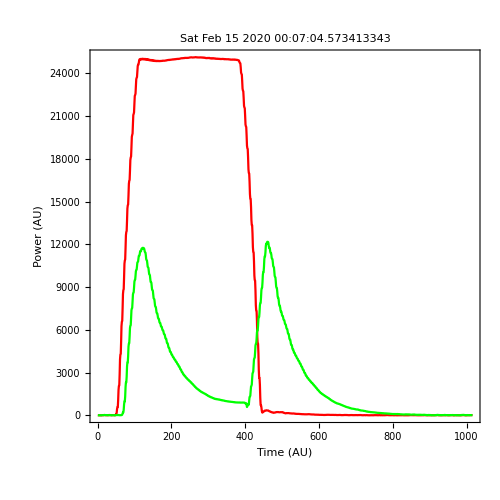
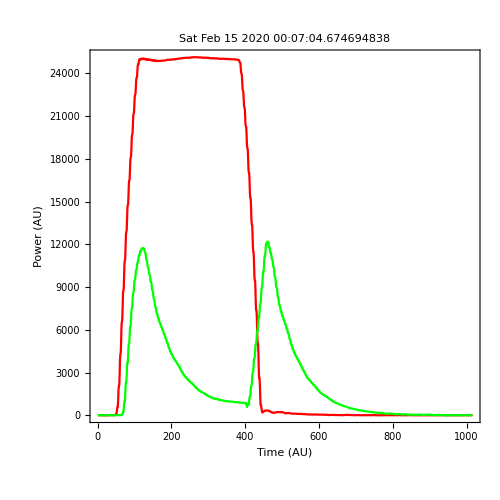
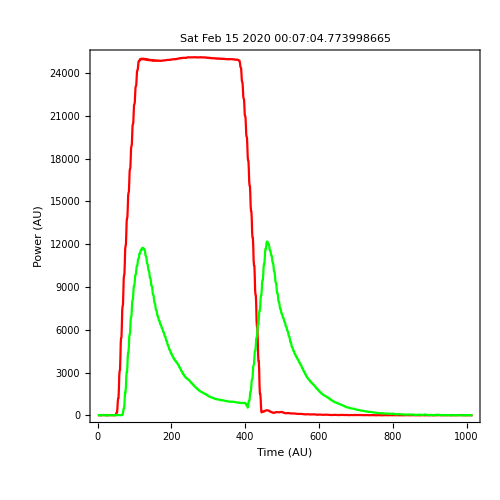
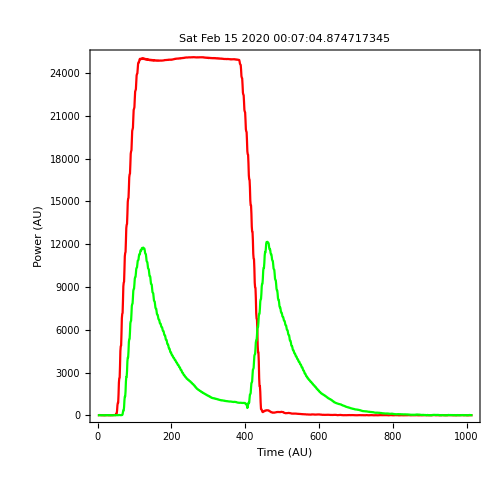
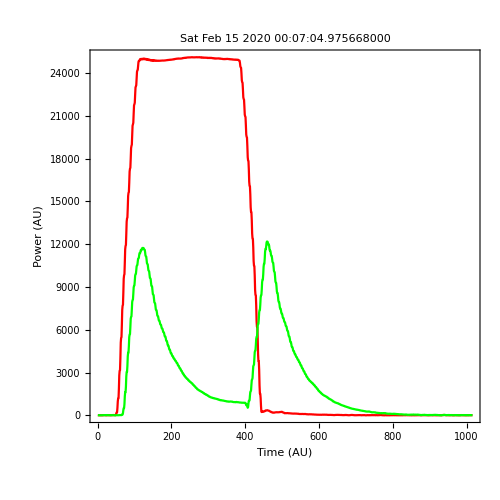
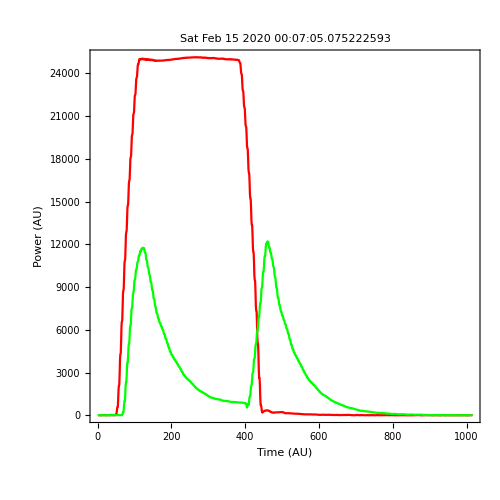
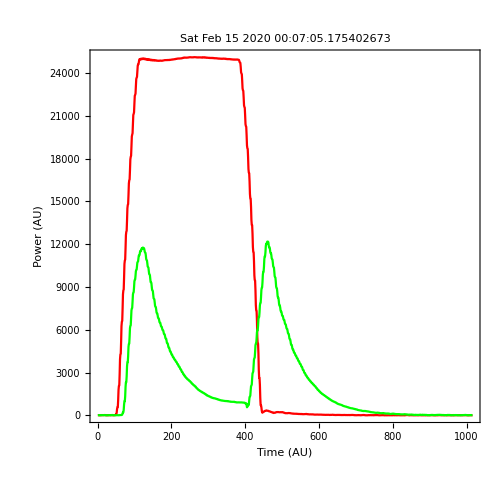
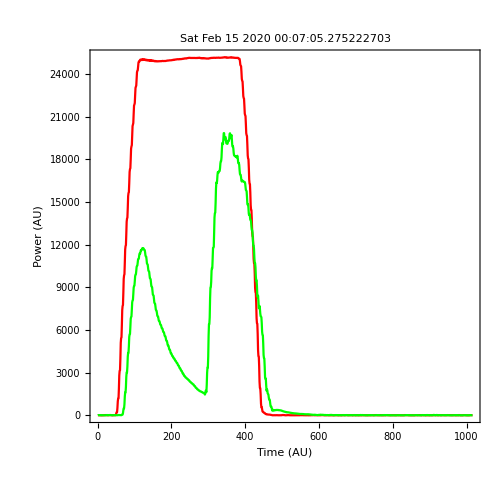

```mathematica
Table[ListPlot[{kfpoplot⟦i⟧,crpoplot⟦i⟧},Joined->True,Frame->True,PlotLabel->crpoplotLabel⟦i⟧,FrameLabel->{"Time (AU)","Power (AU)"},ImageSize->500]
,{i,39,Length@kfpoplot}]
```